Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 1

Metody Rungego-Kutty

Napisać procedury realizujące algorytmy metod Rungego-Kutty rzędu trzeciego i rzędu czwartego (argumenty:  f, x_0, y_0, h, n).

Korzystając z napisanych procedur wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(x y(x) - y^2(x))/x^2,
y(1)=2.

Obliczenia wykonać dla 20 kroków o długości 0.1.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

### Metoda Rungego-Kutty rzędu trzeciego - kod procedury

Wejście: 
	f = f(x,y) - funkcja;
	x0, y0 - wartości;
	n - liczba kroków;
	h - długość kroku.
Wyjście:
	(x_i,y_i) dla i=0,1,...,n - punkty.

```mathematica
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_]:=Module[{yValues,xValues,xNext=x0,yNext=y0,k1,k2,k3},

xValues={x0};
yValues={y0};

Do[
k1=f[xNext,yNext];
k2=f[xNext+h/2,yNext+(h k1)/2];
xNext=xNext+h;
xValues=Append[xValues,xNext];
k3=f[xNext,yNext-h k1+2 h k2];
yNext=yNext+1/6 h (k1+4 k2+k3);
yValues=Append[yValues,yNext],
{i,0,n-1}];

(*Print[{xValues,yValues}];*)
Return[Transpose[{xValues,yValues}]]
]
```

### Metoda Rungego-Kutty rzędu czwartego - kod procedury

Wejście: 
	f = f(x,y) - funkcja;
	x0, y0 - wartości;
	n - liczba kroków;
	h - długość kroku.
Wyjście:
	(x_i,y_i) dla i=0,1,...,n - punkty.

```mathematica
Clear[metodaRK4];
metodaRK4[f_,x0_,y0_,h_,n_]:=Module[{yValues,xValues,xNext=x0,yNext=y0,k1,k2,k3,k4},

xValues={x0};
yValues={y0};

Do[
k1=f[xNext,yNext];
k2=f[xNext+h/2,yNext+(h k1)/2];
k3=f[xNext+h/2,yNext+(h k2)/2];
xNext=xNext+h;
xValues=Append[xValues,xNext];
k4=f[xNext,yNext+h k3];
yNext=yNext+1/6 h (k1+2 k2+2k3+k4);
yValues=Append[yValues,yNext],
{i,0,n-1}];

Return[Transpose[{xValues,yValues}]]
]
```

### Rozwiązanie zagadnienia początkowego

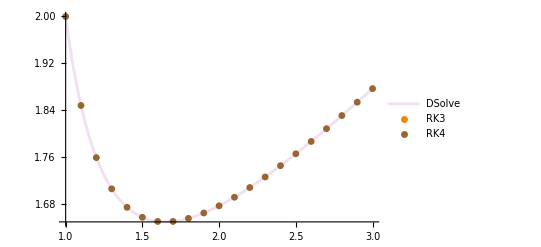

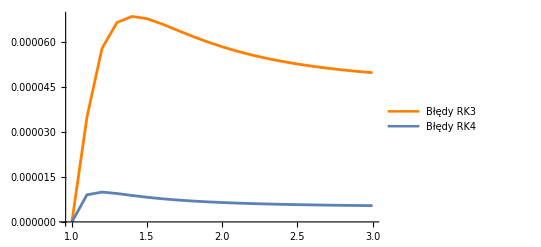

```mathematica
Clear[f,punktyRK3,punktyRK4,solution,RK3,RK4,wykresRK3,wykresRK4,wykresDSolve,x0,y0,h,n,wykresBledyRK3,wykresBledyRK4];
f[x_,y_]:=(x y-y^2)/x^2;
x0=1;
y0=2;
h=0.1;
n=20;
(* Rozwiązanie uzyskane z użyciem procedury DSolve *)
solution=DSolve[{y'[x]==f[x,y[x]],y[1]==2},y[x],x];

(* Rozwiązanie uzyskane z użyciem metodaRK3 *)
punktyRK3=metodaRK3[f,x0,y0,h,n];
wykresRK3=ListPlot[punktyRK3,(*Filling->Axis,*)PlotStyle->Orange,PlotRange->{{.95,3.1},{0.9,2.2}},PlotMarkers->{✶,Large},PlotLegends->{"RK3"}];

(* Rozwiązanie uzyskane z użyciem metodaRK4 *)
punktyRK4=metodaRK4[f,x0,y0,h,n];
wykresRK4=ListPlot[punktyRK4,(*Filling->Axis,*)PlotStyle->Brown,PlotRange->{{.95,3.1},{0.9,2.2}},PlotMarkers->{Automatic,Small},PlotLegends->{"RK4"}];

wykresDSolve=Plot[solution[[1,1,2]],{x,1,3},PlotLegends->{"DSolve"},PlotStyle->LightPurple];

(*Wartości uzyskane z DSolve w węzłach siatki*)
yDSolve=Table[solution[[1,1,2]]/.{x->xw},{xw,x0,x0+h n,h}];

bledyRK3=Table[{punktyRK3[[i,1]],Abs[punktyRK3[[i,2]]-yDSolve[[i]]]},{i,1,n+1}];
wykresBledyRK3=ListPlot[bledyRK3,Joined->True,PlotLegends->{"Błędy RK3"},PlotStyle->{Orange,Thickness[0.005]}];

bledyRK4=Table[{punktyRK4[[i,1]],Abs[punktyRK4[[i,2]]-yDSolve[[i]]]},{i,1,n+1}];
wykresBledyRK4=ListPlot[bledyRK4,Joined->True,PlotLegends->{"Błędy RK4"},PlotStyle->{Thickness[0.005]}];

Show[wykresDSolve,wykresRK3,wykresRK4]
Show[wykresBledyRK3,wykresBledyRK4]
```